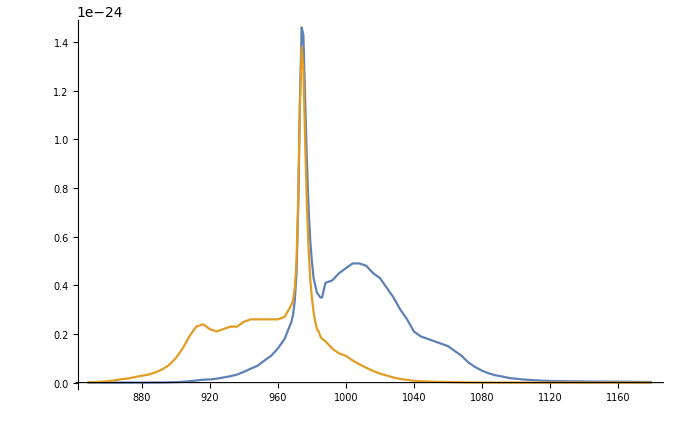

```mathematica
Clear["Global`*"]

(σ=Import[NotebookDirectory[]<>"CrossSection.xls"][[1,5;;,{12,15,16}]])//TableForm;

ListPlot[{σ[[All,{1,2}]],σ[[All,{1,3}]]},Joined->True,PlotRange->All]

σe=Interpolation[σ[[All,{1,2}]]];
σa=Interpolation[σ[[All,{1,3}]]];
```

```mathematica
c=3 10^8;(*м/с*)
τ=1.45 10^-3;(*с*)
NN=300;(*ppm*)
NN=6.62 10^22 NN;(*1/м^3*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

λp=960;(*нм*)
λs=1064;(*нм*)
Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

L=2;

σp12=σa[λp];
σp21=σe[λp];
σs12=σa[λs];
σs21=σe[λs];
```

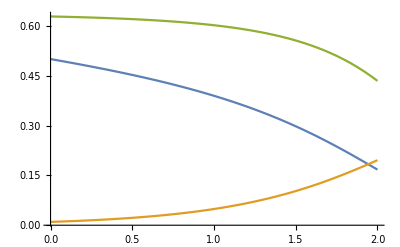

```mathematica
(*Усилитель*)
sol=NDSolve[{ρp[z](σp12 N1[z]-σp21 N2[z])+ρs[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ==0,ρs'[z]==ρs[z](σs21 N2[z]-σs12 N1[z]),ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),N1[z]+N2[z]==NN, Pp ρp[0]==0.5,Ps ρs[0]==10 10^-3},{ρp,ρs,N1,N2},{z,0,L},AccuracyGoal->Infinity];

Plot[Evaluate[{Pp ρp[z],Ps ρs[z],N2[z]/NN}/.sol],{z,0,L},PlotRange->All]
```

{-689.655 N2[z]+(2.6×10^-25 N1[z]-1.4×10^-25 N2[z]) ρp[z]+(1.6×10^-27 N1[z]-1.3×10^-25 N2[z]) ρsl[z]+(1.6×10^-27 N1[z]-1.3×10^-25 N2[z]) ρsr[z]==0,ρsr'[z]==(-1.6×10^-27 N1[z]+1.3×10^-25 N2[z]) ρsr[z],ρsl'[z]==-(-1.6×10^-27 N1[z]+1.3×10^-25 N2[z]) ρsl[z],ρp'[z]==(-2.6×10^-25 N1[z]+1.4×10^-25 N2[z]) ρp[z],N1[z]+N2[z]==1.986×10^25}

{N1[z]→(2.7804 (4.92611×10^27+1. ρp[z]+0.928571 ρsl[z]+0.928571 ρsr[z]))/(689.655+4.×10^-25 ρp[z]+1.316×10^-25 ρsl[z]+1.316×10^-25 ρsr[z]),N2[z]→(5.1636 (1. ρp[z]+0.00615385 ρsl[z]+0.00615385 ρsr[z]))/(689.655+4.×10^-25 ρp[z]+1.316×10^-25 ρsl[z]+1.316×10^-25 ρsr[z])}

{ρsr'[z]==((-21.9145+6.66819×10^-25 ρp[z]+3.30034×10^-41 ρsl[z]+3.30034×10^-41 ρsr[z]) ρsr[z])/(689.655+4.×10^-25 ρp[z]+1.316×10^-25 ρsl[z]+1.316×10^-25 ρsr[z]),ρsl'[z]==-(1. ρsl[z] (-21.9145+6.66819×10^-25 ρp[z]+3.30034×10^-41 ρsl[z]+3.30034×10^-41 ρsr[z]))/(689.655+4.×10^-25 ρp[z]+1.316×10^-25 ρsl[z]+1.316×10^-25 ρsr[z]),ρp'[z]==(ρp[z] (-3561.1+1.83671×10^-40 ρp[z]-6.66819×10^-25 ρsl[z]-6.66819×10^-25 ρsr[z]))/(689.655+4.×10^-25 ρp[z]+1.316×10^-25 ρsl[z]+1.316×10^-25 ρsr[z])}

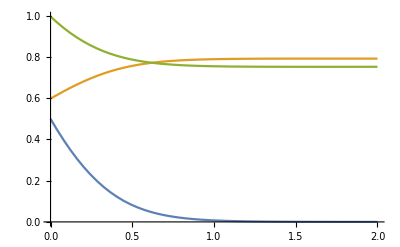

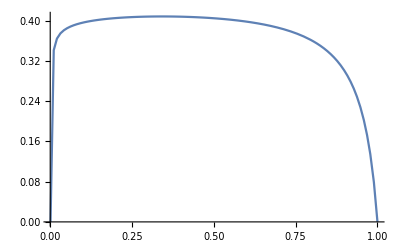

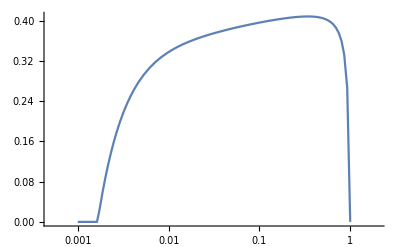

```mathematica
(*Лазер*)
eqns={ρp[z](σp12 N1[z]-σp21 N2[z])+ρsr[z](σs12 N1[z]-σs21 N2[z])+ρsl[z](σs12 N1[z]-σs21 N2[z])-N2[z]/τ==0,
ρsr'[z]==ρsr[z](σs21 N2[z]-σs12 N1[z]),
ρsl'[z]==-ρsl[z](σs21 N2[z]-σs12 N1[z]),
ρp'[z]==ρp[z](σp21 N2[z]-σp12 N1[z]),
N1[z]+N2[z]==NN}

Solve[eqns[[{1,5}]],{N1[z],N2[z]}][[1]]
eqns2=Simplify[eqns[[{2,3,4}]]/.%]

R=0.6;
sol=NDSolve[{eqns2,ρp[0]==0.5/Pp,
0.95ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==20,Ps ρsl[0]==20}}][[1]];

Plot[Evaluate[{ Pp ρp[z],Ps ρsr[z],Ps ρsl[z]}/.sol],{z,0,L},PlotRange->All]

Clear[OutputPower,R]
OutputPower[R_?NumericQ]:=(Ps ρsl[0](1-R))/.(NDSolve[{eqns2,ρp[0]==0.5/Pp,
0.95ρsr[L]==ρsl[L],ρsr[0]==R ρsl[0]},
{ρp,ρsr,ρsl},{z,0,L},AccuracyGoal->-15,Method->{"Shooting","StartingInitialConditions"->{Ps ρsr[0]==20,Ps ρsl[0]==20}}][[1]]);

Plot[OutputPower[R],{R,0.001,1},PlotRange->All,MaxRecursion->1]
LogLinearPlot[OutputPower[R],{R,0.001,1},PlotRange->All,MaxRecursion->1]
```

```mathematica
τ=1.4 10^-3;

NN=300 6.62 10^22;

L=2;

c=3 10^8;(*м/с*)
h=6.63 10^-34;(*Планк*)
Aeff=Pi/4 7^2 10^-12;(*Эффективная площадь моды*)

λs=1060;
λp=960;

σp12=2.6 10^-25;
σp21=1.4 10^-25;
σs12=1.052 10^-25;
σs21=1.683 10^-25;

Ps=Aeff h c/(λs 10^-9);
Pp=Aeff h c/(λp 10^-9);

eq={c/L D[N2[z,t],t]==-N2[z,t]/τ+ρp[z,t](σp12 N1[z,t]-σp21 N2[z,t])+ρs[z,t](σs12 N1[z,t]-σs21 N2[z,t]),
D[ρs[z,t],z]+1/L D[ρs[z,t],t]==ρs[z,t](σs21 N2[z,t]-σs12 N1[z,t]),
D[ρp[z,t],z]+1/L D[ρp[z,t],t]==ρp[z,t](σp21 N2[z,t]-σp12 N1[z,t]),
N1[z,t]+N2[z,t]==NN,
ρs[z,0]==1/Ps Exp[-2 (z-L/3)^2/0.1^2] ,
ρp[z,0]==1000000/Pp Exp[-2 (z-L/2)^2/0.2^2],
N1[z,0]==NN,N2[z,0]==0};

sol=NDSolve[{eq,ρs[L,t]==ρs[0,t],N1[L,t]==N1[0,t],N2[L,t]==N2[0,t]},{ρp,ρs,N1,N2},{z,0,L},{t,0,4},AccuracyGoal->-22,PrecisionGoal->6,NormFunction->1]

Plot3D[Pp ρp[z,t]/.sol,{z,0,L},{t,0,4},PlotPoints->Automatic,MaxRecursion->Automatic,PlotRange->All ]
```

```mathematica
Manipulate[Plot[Pp ρs[z,t]/.sol,{z,0,L},PlotPoints->Automatic,MaxRecursion->Automatic,PlotRange->All],{t,0,4}]
Manipulate[Plot[N2[z,t]/NN/.sol,{z,0,L},PlotPoints->Automatic,MaxRecursion->Automatic,PlotRange->All],{t,0,4}]
```

Домашнее задание 
1) Быть готовым ответить по физике лазера. Характерные точки графика выходной мощности от R, причины возрастания и убывания функции на каждом участке графика.
2) Модель Франца-Нодвика. В среду длиной 3 м с концентрацией ионов 300 ppm, сечением перехода 2.5 пм^2, эффективным диаметром моды 7 мкм падает излучение с длиной волны 1064 нм. Построить график импульса на выходе, энергия в импульсе является параметром задачи. Рассмотреть случай прямоугольного, лоренцева и гауссова импульсов на входе.
3)* Построить функцию, возвращающую среднеквадратичную длительность импульса и его среднюю координату.